# Metrics learned from lattice data

## Ansatz for f(z) and g(z)

### f(z)

This should respect the constraints

Positive: f(z)>0

Asymptotically AdS_5: lim_(z→0) f(z)=1

Horizon at z=1: lim_(z→1) f(z)=0

Satisfy: ∂_z (f(z)/z^4)<0

We enforce the monotonicity explicitly by requiring that
d/(d z)((f(z))/z^4)=-4/z^5a(z)
If we further take
a(z)=1+a_1 z+a_2 z^2+... ,
the resulting f(z) is a simple polynomial (+logarithmic terms). This is good for numerics.
d/(d z)((f(z))/z^4)=-4/z^5a(z)
f(1)-(f(z))/z^4=-∫_z^1 4/x^5 a(x)ⅆx
(f(z))/z^4=f(1)+∫_z^1 4/x^5 a(x)ⅆx .

This is positive if f(1)≥0 and a(z)>0.

It’s asymptotically AdS_5 if a(0)=1, because lim_(z→0) z^4∫_z^1 4/x^5 a(x)ⅆx=a(0).

It vanishes at the horizon if we simply set f(1)=0.

It satisfies ∂_z (f(z)/z^4)<0 by construction for ϵ>0.

Additionally, a(z)=1 corresponds to AdS-BH, because

```mathematica
Assuming[0<z<1,z^4 Integrate[4/x^5,{x,1,z}]]
```

(1-1/z^4) z^4

Therefore,
f(z)=4ϵ ||ā(||)^2(1-z^4)+z^4∫_z^1 4/x^5 a(x)ⅆx .

Note that in overleaf, we write
f(z) = z^4(∫_1)^z 4/x^5 a(x)dx

### g(z)

Positive: g(z)>0 if b(z)>0

Asymptotically AdS_5: lim_(z→0) g(z)=1

Horizon at z=1: lim_(z→1) g(z)=∞

We could use the same g(z) but let’s take an ansatz that is more similar to f(z) which helps with the temperature constraint. Let
g(z)=(b(z))/(1-z^4)=(1+b_1 z+b_2 z^2+...)/(1-z^4) ,
which is positive, asymptotically AdS, and divergent at the horizon.

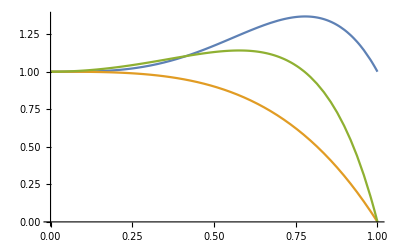

```mathematica
Plot[{1-4 z^4 Log[z],1-z^4+(4(z^4-z^i))/(i+4)/.i->3,(1-z)*(1+z)*(1+z^2)/Exp[Integrate[(a1*x+a2*x^2),{x,0,z}]]/.a1->-1.5/.a2->0},{z,0,1}]
```

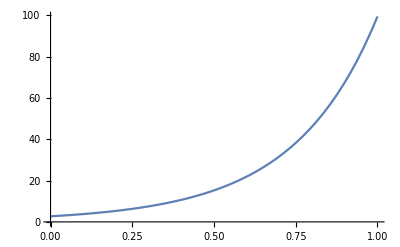

```mathematica
Plot[Exp[1+3.3z+0.3 z^2],{z,0,1}]
```

### Definitions for numerics

```mathematica
f[as_List,z_]:=1-z^4+Sum[as⟦i⟧If[i==4,-4 z^4 Log[z],(4(z^4-z^i))/(i-4)],{i,Length[as]}]
fDer[as_List,z_]:=(4f[as,z])/z-(4(1+as.z^Range[Length[as]]))/z
b[bs_List,z_]:=1+Sum[bs⟦i⟧z^i,{i,Length[bs]}]
g[bs_List,z_]:=b[bs,z]/(1-z^4)
gDer[bs_List,z_]:=(4 z^3)/((1-z^4)^2)b[bs,z]+1/(1-z^4)Sum[i bs⟦i⟧z^(i-1),{i,Length[bs]}]
```

```mathematica
D[f[{a1},z],z]==fDer[{a1},z]//Simplify
D[f[{a1,a2},z],z]==fDer[{a1,a2},z]//Simplify
D[f[{a1,a2,a3},z],z]==fDer[{a1,a2,a3},z]//Simplify
```

True

True

True

```mathematica
D[g[{b1},z],z]==gDer[{b1},z]//Simplify
D[g[{b1,b2},z],z]==gDer[{b1,b2},z]
D[g[{b1,b2,b3},z],z]==gDer[{b1,b2,b3},z]
```

True

True

True

```mathematica
Dimensions[{{{a1},{b1}},{{a2},{b2}},{{a3},{b3}}}]
```

{3,2,1}

```mathematica
MakePlots[as_,bs_]:=GraphicsColumn[{Plot[Evaluate@Table[f[a,z],{a,as}],{z,0,1},AxesLabel->{"z/z_h","f(z/z_h)"},PlotLegends->Table["N="<>ToString[i],{i,Length[as]}]],Plot[Evaluate@Table[g[a,z],{a,as}],{z,0,1},AxesLabel->{"z/z_h","g(z/z_h)"},PlotLegends->Table["N="<>ToString[i],{i,Length[as]}]]}]
```

```mathematica
MakePlots[{{0,0,0,Exp@-0.12,Exp@0.26}},{{0,0,0,2.9,3.6}}]
```

-Graphics-

## Metrics from data

The metrics will be different depending on how many parameters were used in the ansätze.

### T=113 MeV

### T=226 MeV

#### N=1

a={0,0,0,31.21250243}
b={0,0,0,6.61940835}
R^2/(2π α')=0.18644167624802452
shift=10.450073849281361
loss=64.37066461745157

#### N=2

a={0,0,0,38.51757998, 10.64963975}
b={0,0,0,10.63105693,-3.7697443}
R^2/(2π α')=0.20666911020368492
shift=11.697387880683888
loss=46.06748808533031

#### N=3

a={0,0,0,45.4692875,24.16283525,14.83428022}
b={0,0,0,21.35840796,-4.98297874,-7.43777914}
R^2/(2π α')=0.21434089742662638
shift=13.958214694956487
loss=39.28062068055563

```mathematica
MakePlots[{{0,0,0,31.21250243},{0,0,0,38.51757998, 10.64963975},{0,0,0,45.4692875,24.16283525,14.83428022}},{{0,0,0,6.61940835},{0,0,0,10.63105693,-3.7697443},{0,0,0,21.35840796,-4.98297874,-7.43777914}}]
```

-Graphics-

### T=254 MeV

#### N=1

a={0,0,0,25.81526085}
b={0,0,0,5.46843766}
R^2/(2π α')=0.17433520280392675
shift=8.674968137808108
loss=58.66031660432106

#### N=2

a={0,0,0,39.84200949, 18.9141639}
b={0,0,0,14.59782938,-7.54112889}
R^2/(2π α')=0.18589928608611322
shift=10.58302254268101
loss=28.5288881175364

#### N=3

```mathematica
Exp[20]//N
```

4.85165×10^8

a={0,0,0,41.12845971,20.02559773,-0.39794211}
b={0,0,0,17.71964093,-7.98528673,-2.56518331}
R^2/(2π α')=0.18550375913719336
shift=10.85426309802883
loss=27.9534621983376

```mathematica
MakePlots[{{0,0,0,25.81526085},{0,0,0,39.84200949, 18.9141639},{0,0,0,41.12845971,20.02559773,-0.39794211}},{{0,0,0,5.46843766},{0,0,0,14.59782938,-7.54112889},{0,0,0,17.71964093,-7.98528673,-2.56518331}}]
```

-Graphics-

### T=271 MeV

#### N=1

a={0,0,0,38.28305482}
b={0,0,0,4.13876371}
R^2/(2π α')=0.19531389640591124
shift=8.614922292240353
loss=39.24613847674415

#### N=2

a={0,0,0,49.55307557, 15.65704209}
b={0,0,0,12.53269759,-7.42427439}
R^2/(2π α')=0.20189555306786844
shift=9.912294823954696
loss=29.58533522356293

#### N=3

a={0,0,0,65.05550428,47.09770985,30.50219846}
b={0,0,0,38.69394602,-11.79670732,-19.04062508}
R^2/(2π α')=0.20798937829156983
shift=13.355123215101585
loss=26.737792303241214

```mathematica
MakePlots[{{0,0,0,38.28305482},{0,0,0,49.55307557, 15.65704209},{0,0,0,65.05550428,47.09770985,30.50219846}},{{0,0,0,4.13876371},{0,0,0,12.53269759,-7.42427439},{0,0,0,38.69394602,-11.79670732,-19.04062508}}]
```

-Graphics-

### T=290 MeV

#### N=1

a={0,0,0,6.75860577}
b={0,0,0,3.73283857}
R^2/(2π α')=0.14980087974033215
shift=5.71468557614725
loss=2.1931109898671917

#### N=2

a={0,0,0,-3.82235551, 8.0571461}
b={0,0,0,7.42589798,-4.99426863}
R^2/(2π α')=0.18982148544551058
shift=5.557101010126762
loss=1.321227000927049

#### N=3

a={0,0,0,-4.68520164,7.68199322,0.38636144}
b={0,0,0,9.53890053,-5.1963552,-2.18673599}
R^2/(2π α')=0.19569989830129791
shift=5.505301505475836
loss=1.2394866367657005

```mathematica
MakePlots[{{0,0,0,6.75860577},{0,0,0,-3.82235551, 8.0571461},{0,0,0,-4.68520164,7.68199322,0.38636144}},{{0,0,0,3.73283857},{0,0,0,7.42589798,-4.99426863},{0,0,0,9.53890053,-5.1963552,-2.18673599}}]
```

-Graphics-

### T=312 MeV

#### N=1

a={0,0,0,7.99921986}
b={0,0,0,2.43295497}
R^2/(2π α')=0.16036044041170358
shift=5.319476474355767
loss=17.054945154580118

#### N=2

a={0,0,0,6.32367679, 0.35583276}
b={0,0,0,2.94597239,-0.93471662}
R^2/(2π α')=0.16688777833710955
shift=5.2162925820093635
loss=16.417274528742443

#### N=3

a={0,0,0,5.14421884,0.30098459,0.79166906}
b={0,0,0,3.74424423,-0.8975631,-0.70735762}
R^2/(2π α')=0.16541626477830684
shift=5.190110032339777
loss=15.181365586634678

```mathematica
MakePlots[{{0,0,0,7.99921986},{0,0,0,6.32367679, 0.35583276},{0,0,0,5.14421884,0.30098459,0.79166906}},{{0,0,0,2.43295497},{0,0,0,2.94597239,-0.93471662},{0,0,0,3.74424423,-0.8975631,-0.70735762}}]
```

-Graphics-

### T=338 MeV

#### N=1

a={0,0,0,4.7014027}
b={0,0,0,1.43387272}
R^2/(2π α')=0.16612382274632798
shift=4.454590902369131
loss=18.99515374243721

#### N=2

a={0,0,0,5.72359559,-0.92655933}
b={0,0,0,1.35337084,0.14344181}
R^2/(2π α')=0.1627214603738293
shift=4.457023134624758
loss=18.963192834783055

#### N=3

a={0,0,0,4.9230029,-2.27325142, 0.91265099}
b={0,0,0,3.1331106,1.00128251,-2.92269615}
R^2/(2π α')=0.16536153505996765
shift=4.401510838530424
loss=17.758420146946616

```mathematica
MakePlots[{{0,0,0,4.7014027},{0,0,0,5.72359559,-0.92655933},{0,0,0,4.9230029,-2.27325142, 0.91265099}},{{0,0,0,1.43387272},{0,0,0,1.35337084,0.14344181},{0,0,0,3.1331106,1.00128251,-2.92269615}}]
```

-Graphics-

with std = 0.5 and N=2, I get

#### N=2

a={0,0,0,0.70266306,-0.82645481}
b={0,0,0,3.04547813,3.04195875}
R^2/(2π α')=0.0961069625742916
shift=4.322974836167359
loss=0.7693461471585007

### T=369 MeV

#### N=1

a={0,0,0,4.92535553}
b={0,0,0,0.47267591}
R^2/(2π α')=0.18460893583996157
shift=4.129566732530089
loss=18.902927673636754

#### N=2

a={0,0,0,4.78197955,-1.65020884}
b={0,0,0,6.17626559,-5.84242327}
R^2/(2π α')=0.17759191082730638
shift=4.057931351729718
loss=17.469877927446948

#### N=3

a={0,0,0,3.93458911,-2.36721932, 0.83866427}
b={0,0,0,7.57747607,-5.89726604,-1.43668585}
R^2/(2π α')=0.18083850588297307
shift=4.012666396429069
loss=17.01998694600411

```mathematica
MakePlots[{{0,0,0,4.92535553},{0,0,0,4.78197955,-1.65020884},{0,0,0,3.93458911,-2.36721932, 0.83866427}},{{0,0,0,0.47267591},{0,0,0,6.17626559,-5.84242327},{0,0,0,7.57747607,-5.89726604,-1.43668585}}]
```

-Graphics-

### T=406 MeV

#### N=1

a={0,0,0,2.48054754}
b={0,0,0,-0.15437361}
R^2/(2π α')=0.194062
shift=3.443738861691576
loss=17.879493

#### N=2

a={0,0,0,4.36064617,-2.24123082}
b={0,0,0,1.96009883,-2.13899549}
R^2/(2π α')=0.18550104350472185
shift=3.4485045122209175
loss=15.078335584094425

#### N=3

a={0,0,0,5.66284654,-3.45883237,-0.60852597}
b={0,0,0,4.15352104-1.99406588-2.39107614}
R^2/(2π α')=0.1759059901418243
shift=3.4568794203962896
loss=13.91595708071366

```mathematica
MakePlots[{{0,0,0,2.48054754},{0,0,0,4.36064617,-2.24123082},{0,0,0,5.66284654,-3.45883237,-0.60852597}},{{0,0,0,-0.15437361},{0,0,0,1.96009883,-2.13899549},{0,0,0,4.15352104-1.99406588-2.39107614}}]
```

-Graphics-

## Horizon temperature

T=1/(4π)√(f' (1/g)')/.z->zh (=1)

```mathematica
1/(4π)√(D[f[{0,0,0,Exp@0.71,Exp@0.8},z],z]D[1/g[{0,0,0,3.1,3.4},z],z])
%/.z->1
```

1/(4 π)(√((-((1-z^4) (12.4 z^3+17. z^4))/((1+3.1 z^4+3.4 z^5)^2)-(4 z^3)/(1+3.1 z^4+3.4 z^5)) (-12.136 z^3+8.90216 (4 z^3-5 z^4)-32.5439 z^3 Log[z])))

0.266559

```mathematica
1/(4π)√(D[f[{0,0,0,5.72359559,-0.92655933},z],z]D[1/g[{0,0,0,1.35337084,0.14344181},z],z])
%/.z->1
```

1/(4 π)(√((-((1-z^4) (5.41348 z^3+0.717209 z^4))/((1+1.35337 z^4+0.143442 z^5)^2)-(4 z^3)/(1+1.35337 z^4+0.143442 z^5)) (-26.8944 z^3-3.70624 (4 z^3-5 z^4)-91.5775 z^3 Log[z])))

0.485021

QuiverEE todo:
1) def for central charge without ref to EE? namely, from other sources and then compare to  ours. take (8.9) of https://arxiv.org/pdf/1503.07527.pdf and compare to liu-mezei of 1.21 in our overleaf quiverEE file (need to take domain wall crdts?)
2) Wait for the background form carlos, then start working on the confining case
what we can already try, is in our overleaf file, solve 1.24, plug in to 1.22 and take the liu-mezei derivatives (see how well numerics work out)